# Calculus

## Revision and Introduction

## Plotting

```mathematica
Clear[x]
```

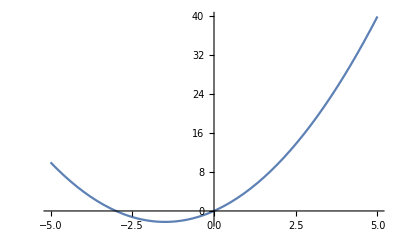

```mathematica
Plot[x^2+3x,{x,-5,5}]
```



```mathematica
Plot[Sin[t],{t,0,2Pi}]
```

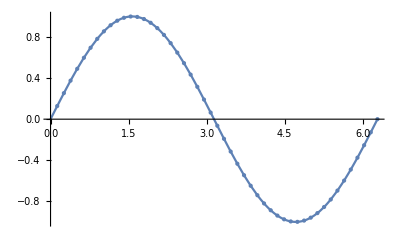

```mathematica
Plot[Sin[theta],{theta,0,2 Pi},Mesh->Full]
```

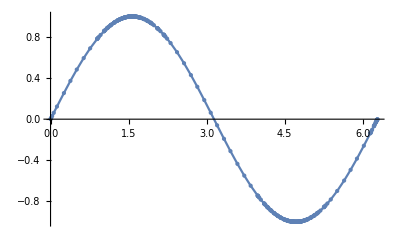

```mathematica
Plot[Sin[theta],{theta,0,2 Pi},Mesh->All]
```

## Multiple Plots

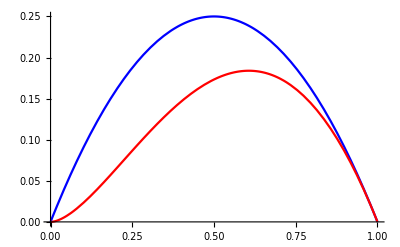

```mathematica
Plot[{y-y^2,-y^2*Log[y]},{y,0,1},PlotStyle->{Blue,Red}]
```

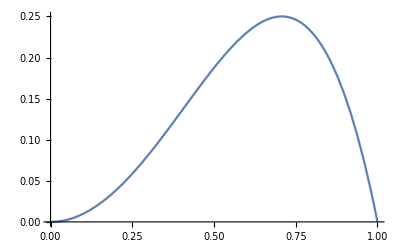

```mathematica
plot1=Plot[y^2-y^4,{y,0,1}]
```

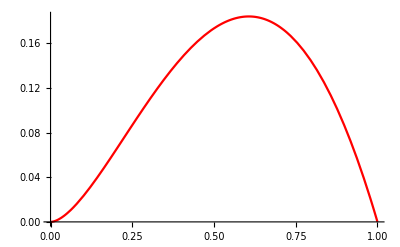

```mathematica
plot2=Plot[-y^2*Log[y],{y,0,1},PlotStyle->Red]
```

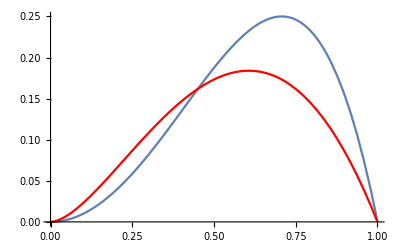

```mathematica
Show[plot1,plot2]
```

## Limits

```mathematica
Limit[1/k,k->Infinity]
```

0

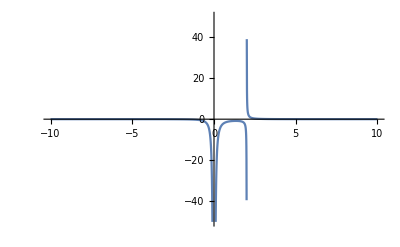

```mathematica
Plot[1/(x^3-2x^2),{x,-10,10},PlotRange->50]
```

```mathematica
With[{p=1/(x^3-2x^2)}, 
Limit[p,{x->0}]
]
```

-∞

```mathematica
f[x_]:=x*Sin[Pi*x]+2*Tanh[x-5]
```

```mathematica
Limit[f[x],x->Infinity]
```

Indeterminate

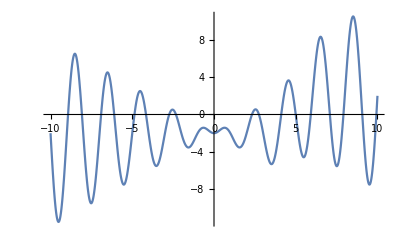

```mathematica
Plot[f[x],{x,-10,10}]
```

## Differentiation

```mathematica
ClearAll["Global`*"]
```

```mathematica
D[x^2,x]
D[Sin[x],x] 
D[t^2+t+1,t] 
D[ⅇ^(2 var),var]
```

2 x

Cos[x]

1+2 t

2 ⅇ^(2 var)

```mathematica
D[t^2+t+1,{t,2}]
```

2

```mathematica
Cos '[x]
```

-Sin[x]

## Integration

```mathematica
Integrate[x,{x,1,3}] 
Integrate[Sin[x],x]
```

4

-Cos[x]

```mathematica
ClearAll[x]
```

```mathematica
fx:=Sin[x];
```

```mathematica
plot1=Plot[fx,{x,-π,π}];
```

```mathematica
gx=Integrate[fx,x]
```

-Cos[x]

```mathematica
plot2=Plot[gx,{x,-π,π}];
```

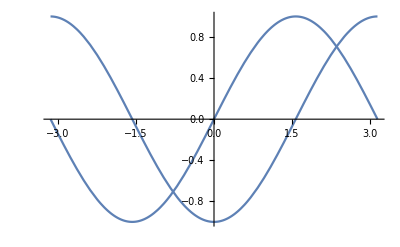

```mathematica
Show[plot1,plot2]
```